# 1R Free Throw Gerik Zatorski

```mathematica
Quit[];
(*
TODO:
Is 0 optimized or should I change it to 0.?
*)
```

## Kinematics of Shot

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

-(43 π)/30

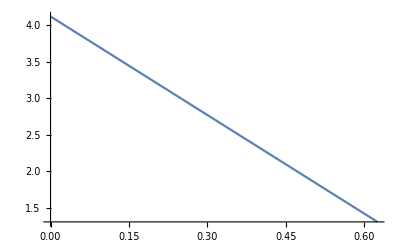

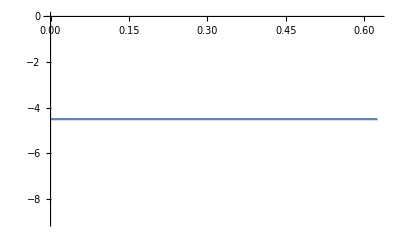

```mathematica
ClearAll["Global`*"]

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Helpers *)
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};
getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]
getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]
getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]
getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]
getAllVariables[other_]:=other
extractVariables[formula_]:=With[{pat=_Symbol[___][___]|Subscript[_Symbol,__][___]|Subscript[_Symbol,__]|_Symbol},Union@Cases[formula,pat,-1]]

(* Conversions *)
FtToM=0.3048;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* Robot Link Lengths Constants *)
Lhand=0.3048*8.5/12;

(* World to Joint Frame Transformations *)
gwrist=g[2,0,0].g[0,0,θwrist[t]];
ghand=gwrist.g[Lhand/2,0,0];
gfingertip=gwrist.g[Lhand,0,0].g[0,0,0];

(* World to Ball Frame Transformations prior to roll*)
gballbefore=gwrist.g[Lhand/2,-rball,0];
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];

(* Joint Velocities *)
tMax =5/8;
θwristsol=ListInterpolation[{Pi*21/16,Pi*5/12},{0,tMax}][t];
(*θwristsol=ListInterpolation[{Pi*21/16,Pi*21/16},{0,tMax}][t];*)
(*θwristsol=Interpolation[Table[{{t},-3*Sin[t]+Pi*21/16,-Cos[t]},{t,0,2,0.05}]][t]*)
θwristdotsol=D[θwristsol,t];
θwristdotdotsol=D[θwristdotsol,t];
θwrist[t]=θwristsol;
θwrist'[t]=θwristdotsol;

(*********************************** Shot Animation ****************************************)
coordwrist[time_]:=({gwrist[[1,3]],gwrist[[2,3]]})/.t->time;
coordfingertip[time_]:=({gfingertip[[1,3]],gfingertip[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;

(* goint Graphics *)
Graphicshand=Line[{coordwrist[t],coordfingertip[t]}];

(* Ball Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

(* Solving for conditions at roll *)
troll=0;
tr=gballbefore/.{θwrist[t]->θwristsol};
xr=tr[[1,3]]/.t->troll;
yr=tr[[2,3]]/.t->troll;
θr=θwrist[t]/.{θwrist[t]->θwristsol}/.t->troll;
(*θr=N[ArcCos[tr[[1,1]]]];*)

(* dot sol estimation *)
(*tr1=gballbefore/.{θwrist[t]->θwristsol}/.t->(troll-.01);
tr2=gballbefore/.{θwrist[t]->θwristsol}/.t->(troll+.01);
θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr1[[1,1]]])/.02]
xrdot=N[(tr2[[1,3]]-tr1[[1,3]])/.02]
yrdot=N[(tr2[[2,3]]-tr1[[2,3]])/.02]*)
(*θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr[[1,1]]])/.01]
xrdot=N[(tr2[[1,3]]-tr[[1,3]])/.01]
yrdot=N[(tr2[[2,3]]-tr[[2,3]])/.01]*)

(* dot sol exact *)
θrdot=θwristdotsol/.t->troll
trdot=D[gballbefore,t]/.{θwrist[t]->θwristsol,θwrist'[t]->θwristdotsol};
(*trdot=D[gballbefore,t];*)
xrdot=trdot[[1,3]]/.t->troll;
yrdot=trdot[[2,3]]/.t->troll;

(* Plots *)
Plot[θwristsol,{t,0,tMax}]
Plot[θwristdotsol,{t,0,tMax}]

(* Animations *)
Animate[
Show[
Graphics[{
Black,Graphicshand/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
},Axes->True]
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```

## roll constraint and roll off “fingertips”

-(21 π)/16+θ[0]

Let it fly!

0.228421

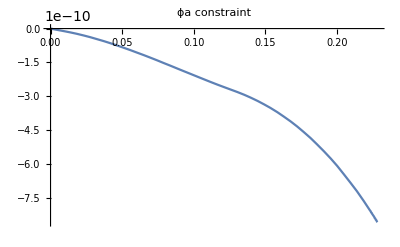

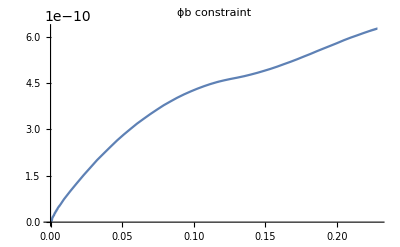

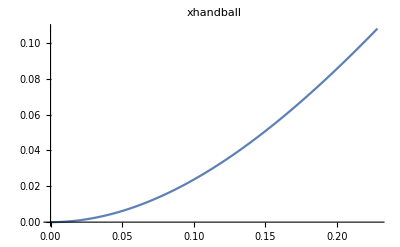

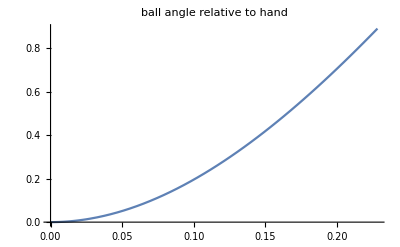

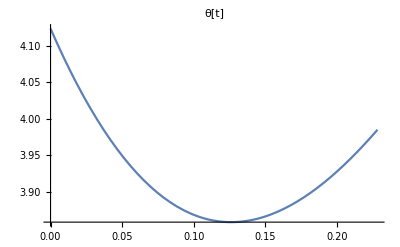

```mathematica
(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],0].g[0,0,θ[t]];
ghandball=Inverse[ghand].gball; (* ball in hand frame *)
θhandball=θ[t]-θwrist[t];
xhandball=ghandball[[1,3]];
gcontact=gwrist.g[Lhand/2-rball*θhandball,0,0];
 
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,J}];
J=m*rball^2;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(***************************************************************************)
(* Constraints and External forces *)
(***************************************************************************)

(* Point of contact *)
mhand=(gfingertip[[2,3]]-gwrist[[2,3]])/(gfingertip[[1,3]]-gwrist[[1,3]]);
Eqhand=contacty-gfingertip[[2,3]]==mhand*(contactx-gfingertip[[1,3]]);
Eqprojection=contacty-gball[[2,3]]==-1/mhand*(contactx-gball[[1,3]]);
contacttemp=Solve[{Eqhand&&Eqprojection},{contactx,contacty}];
contactx=contacttemp[[1,1,2]];
contacty=contacttemp[[1,2,2]];

(* Constraints *)
(* Ball remains in contact with last link *)
ϕa=ghandball[[2,3]]+rball;

(* Ball rolls without slipping where x=rball*θ *)
ϕb=xhandball-rball*θhandball;

(* gotta do this *)
(*θwrist[t]=θwristsol;
θwrist'[t]=θwristdotsol;
θwrist''[t]=θwristdotdotsol;*)

(***************************************************************************)
(* Euler-Lagrange equations VECTORS *)
(***************************************************************************)

(* BOTH constraints *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
Eq5=D[D[ϕb,t],t]==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4&&Eq5},{x''[t],y''[t],θ''[t],λa,λb}];

EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants and Initial Condition *)
grav = 9.8;
InitCon={x[troll]==xr,y[troll]==yr,θ[troll]==θr,x'[troll]==xrdot,y'[troll]==yrdot,θ'[troll]==θrdot};

(***************************************************************************)
(* Numerical Solutions *)
(***************************************************************************)

(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tMax}];*)
(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];*)
(*θhandball/.t->0*)

Jwrist=θwristsol/.t->time;
tRelease=0;
sol=NDSolve[Join[EL,InitCon,
(* determine time of release *)
{WhenEvent[rball*(θ[t]-Jwrist/.time->t)>Lhand/2,
{Print["Let it fly!"],tRelease=t,Print[tRelease],"StopIntegration"},
"DetectionMethod"->"Sign"]}
],{x,y,θ},{t,troll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->3}];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

(***************************************************************************)
(* PLOTS AND ANIMATION *)
(***************************************************************************)

Plot[ϕa/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ϕa constraint"]
Plot[ϕb/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ϕb constraint"]
Plot[(xhandball)/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"xhandball"]
Plot[θhandball/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ball angle relative to hand"]
Plot[θ[t]/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"θ[t]"]

(* Dynamic coords and graphics *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordcontact[time_]:=({contactx,contacty}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
gmidline1=gball.g[-rball,0,0];
gmidline2=gball.g[rball,0,0];
coordmidline1[time_]:=({gmidline1[[1,3]],gmidline1[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordmidline2[time_]:=({gmidline2[[1,3]],gmidline2[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicscontact=Locator[{coordcontact[t][[1]][[1]],coordcontact[t][[2]][[1]]}];
Graphicsballline=Line[{{coordmidline1[t][[1]][[1]],coordmidline1[t][[2]][[1]]},{coordmidline2[t][[1]][[1]],coordmidline2[t][[2]][[1]]}}];

Animate[
Show[
Graphics[{
Black,Graphicshand/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Graphicscontact/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,troll,tRelease},
AnimationRunning->False,
AnimationRate->1.0
]
```